```mathematica
Clear["Global`*"]
```

# Some GW strain calculations

## “Hot Jupiters” from the exoplanet database.

Spot check a couple of them.
HD 21707  orb per 7.1d  1.4 MassJ  1.0 MassSun 19.7 pc
GJ 876 orb per 61d 2.3 MassJ 0.33 MassSun  4.7 pc

Some constants.

```mathematica
massSun = 1.99 10^30; (*kg *)massJ = 1.9 10^27; (* kg *)
massE = 5.97 10^24; (* kg *)
massJe = 317.9; (* earth masses *)
massJs = massJ/massSun; (* relative to the sun's mass *)
pc = 30.86 10^15; (* meters, parsec *)
au = 149.6 10^9; (* meters, astron unit *)
cee = 299792458.0; (* meters/s, speed of light *)
rscon = 3000.0; (* meters per solar mass, Schwarzschild radius *)
rscon = 2*6.67388 10^-11*massSun/cee^2 (* solar mass Scharzschild radius *)
lunits =6.67388 10^-11*massSun/cee^2 (* meters per solar mass, units of G=c=1 *)
```

2955.43

```mathematica
massJs
```

0.000954774

```mathematica
1/massJs
```

1047.37

Some Formulae.  Use Kepler to find the separation in au given the period in days.  The other two are the “normalized” hzero and omega squared divided by c squared from

```mathematica
Text[Style[
    ToExpression["\\sin\\alpha", TeXForm, HoldForm], Large] ]
```

sin α

```mathematica
Text[Style[ToExpression[
"h_0 = \\frac{r_{s1}\\ r_{s2}}{r\\cdot R}",TeXForm,HoldForm],Large] ]
```

h_0==(r_(s 1) r_(s 2))/(r·R)

```mathematica
Text[Style[ToExpression[
"{{\\omega_s^2}\\over{c^2}}  = \\frac{r_{s1} + r_{s2}}{2\\ R^3}",TeXForm,HoldForm],Large] ]
```

ω_s^2/c^2==(r_(s 1)+r_(s 2))/(2 R^3)

```mathematica
sepAU[days_]:=(days/365.24)^(2/3)
(* Test for Null values and return -9999.99 . *)
calchzero[plorbper_, plbmassj_, stmass_, stdist_]:=
plbmassj*massJs*rscon*stmass*rscon/( sepAU[plorbper]*au*stdist*pc )
calcωsq[plorbper_, plbmassj_, stmass_]:=
(plbmassj*massJs+stmass)*rscon/2/(sepAU[plorbper]*au)^3  (* really (ω/c)^2, like k *)
```

### HD 21707 orb per 7.1d 1.4 MassJ 1.0 MassSun 19.7 pc

```mathematica
bigR = sepAU[7.1]*au
rs1 = rscon*1.4*massJs
rs2 = rscon*1.0
dist = 19.7*pc
hzero = rs1*rs2/(dist*bigR); Print["hzero = ", hzero]
omegasovercee = Sqrt[ (rs1 + rs2)/2/bigR^3 ]
freq = 2*omegasovercee*cee/2/Pi; Print["freq (Hz) = ", freq]
```

1.08156×10^10

3.95047

2955.43

6.07942×10^17

hzero = 1.77564×10^-24

3.41985×10^-14

freq (Hz) = 3.26346×10^-6

Check that the functions give the same.

```mathematica
{calchzero[7.1, 1.4, 1.0, 19.7], 2*Sqrt[calcωsq[7.1, 1.4, 1.0]]*cee/2/Pi}
```

{1.77564×10^-24,3.26346×10^-6}

### GJ 876 orb per 61d 2.3 MassJ 0.33 MassSun 4.7 pc

```mathematica
bigR = sepAU[61]*au
rs1 = rscon*2.3*massJs
rs2 = rscon*0.33
dist = 4.7*pc
hzero = rs1*rs2/(dist*bigR); Print["hzero = ", hzero]
omegasovercee = Sqrt[ (rs1 + rs2)/2/bigR^3 ]
freq = 2*omegasovercee*cee/2/Pi; Print["freq (Hz) = ", freq]
```

4.53697×10^10

6.49006

975.291

1.45042×10^17

hzero = 9.61884×10^-25

2.29268×10^-15

freq (Hz) = 2.18783×10^-7

## Read the planets_filtered.csv file.

Has 75 rows starting with # that give the columns and other info.  Column headers in Row number 75, then data as strings??

```mathematica
alldata = Import["/scratch/gabella/Documents/astro/exop/planets_filtered.csv"];
```

```mathematica
alldata[[75;;80]]
```

{{#},{rowid,pl_hostname,pl_letter,pl_discmethod,pl_pnum,pl_orbper,pl_orbpererr1,pl_orbpererr2,pl_orbperlim,pl_orbsmax,pl_orbsmaxerr1,pl_orbsmaxerr2,pl_orbsmaxlim,pl_orbeccen,pl_orbeccenerr1,pl_orbeccenerr2,pl_orbeccenlim,pl_orbincl,pl_orbinclerr1,pl_orbinclerr2,pl_orbincllim,pl_bmassj,pl_bmassjerr1,pl_bmassjerr2,pl_bmassjlim,pl_bmassprov,pl_radj,pl_radjerr1,pl_radjerr2,pl_radjlim,pl_dens,pl_denserr1,pl_denserr2,pl_denslim,pl_ttvflag,pl_kepflag,pl_k2flag,pl_nnotes,ra_str,ra,dec_str,dec,st_dist,st_disterr1,st_disterr2,st_distlim,st_optmag,st_optmagerr,st_optmaglim,st_optmagblend,st_optband,st_teff,st_tefferr1,st_tefferr2,st_tefflim,st_teffblend,st_mass,st_masserr1,st_masserr2,st_masslim,st_massblend,st_rad,st_raderr1,st_raderr2,st_radlim,st_radblend,rowupdate},{340,HD 160691,b,Radial Velocity,4,643.25,0.9,-0.9,0,1.497,,,0,0.128,0.017,-0.017,0,,,,,1.08,,,0,Msini,,,,,,,,,0,0,0,0,17h44m08.70s,266.036,-51d50m02.6s,-51.8341,15.28,0.18,-0.19,0,5.15,,0,0,V (Johnson),5807.,30.,-30.,0,0,1.08,0.05,-0.05,0,0,,,,,0,2014-08-21},{312,HD 147513,b,Radial Velocity,1,528.4,6.3,-6.3,0,1.32,,,0,0.26,0.05,-0.05,0,,,,,1.21,,,0,Msini,,,,,,,,,0,0,0,0,16h24m01.29s,246.005,-39d11m34.7s,-39.193,12.87,0.14,-0.14,0,5.39,,0,0,V (Johnson),5883.,,,0,0,1.11,,,0,0,,,,,0,2014-05-14},{439,HD 217107,b,Radial Velocity,2,7.12682,0.000039,-0.000039,0,0.0748,0.0043,-0.0043,0,0.1267,0.0052,-0.0052,0,,,,,1.39,0.11,-0.11,0,Msini,,,,,,,,,0,0,0,0,22h58m15.54s,344.565,-02d23m43.4s,-2.39539,19.72,0.29,-0.3,0,6.16,,0,1,V (Johnson),5646.,,,0,0,1.02,,,0,0,,,,,0,2014-05-14},{472,HD 27442,b,Radial Velocity,1,428.1,1.1,-1.1,0,1.271,0.073,-0.073,0,0.06,0.043,-0.043,0,,,,,1.56,0.14,-0.14,0,Msini,,,,,,,,,0,0,0,0,04h16m29.03s,64.121,-59d18m07.8s,-59.3022,18.24,0.17,-0.17,0,4.44,,0,0,V (Johnson),4846.,44.,-44.,0,0,1.23,,,0,0,,,,,0,2014-07-23}}

```mathematica
alldata[[77]]
```

{340,HD 160691,b,Radial Velocity,4,643.25,0.9,-0.9,0,1.497,,,0,0.128,0.017,-0.017,0,,,,,1.08,,,0,Msini,,,,,,,,,0,0,0,0,17h44m08.70s,266.036,-51d50m02.6s,-51.8341,15.28,0.18,-0.19,0,5.15,,0,0,V (Johnson),5807.,30.,-30.,0,0,1.08,0.05,-0.05,0,0,,,,,0,2014-08-21}

```mathematica
alldata[[76;;]]//TableForm
```

rowid | pl_hostname | pl_letter | pl_discmethod | pl_pnum | pl_orbper | pl_orbpererr1 | pl_orbpererr2 | pl_orbperlim | pl_orbsmax | pl_orbsmaxerr1 | pl_orbsmaxerr2 | pl_orbsmaxlim | pl_orbeccen | pl_orbeccenerr1 | pl_orbeccenerr2 | pl_orbeccenlim | pl_orbincl | pl_orbinclerr1 | pl_orbinclerr2 | pl_orbincllim | pl_bmassj | pl_bmassjerr1 | pl_bmassjerr2 | pl_bmassjlim | pl_bmassprov | pl_radj | pl_radjerr1 | pl_radjerr2 | pl_radjlim | pl_dens | pl_denserr1 | pl_denserr2 | pl_denslim | pl_ttvflag | pl_kepflag | pl_k2flag | pl_nnotes | ra_str | ra | dec_str | dec | st_dist | st_disterr1 | st_disterr2 | st_distlim | st_optmag | st_optmagerr | st_optmaglim | st_optmagblend | st_optband | st_teff | st_tefferr1 | st_tefferr2 | st_tefflim | st_teffblend | st_mass | st_masserr1 | st_masserr2 | st_masslim | st_massblend | st_rad | st_raderr1 | st_raderr2 | st_radlim | st_radblend | rowupdate
340 | HD 160691 | b | Radial Velocity | 4 | 643.25 | 0.9 | -0.9 | 0 | 1.497 |  |  | 0 | 0.128 | 0.017 | -0.017 | 0 |  |  |  |  | 1.08 |  |  | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 17h44m08.70s | 266.036 | -51d50m02.6s | -51.8341 | 15.28 | 0.18 | -0.19 | 0 | 5.15 |  | 0 | 0 | V (Johnson) | 5807. | 30. | -30. | 0 | 0 | 1.08 | 0.05 | -0.05 | 0 | 0 |  |  |  |  | 0 | 2014-08-21
312 | HD 147513 | b | Radial Velocity | 1 | 528.4 | 6.3 | -6.3 | 0 | 1.32 |  |  | 0 | 0.26 | 0.05 | -0.05 | 0 |  |  |  |  | 1.21 |  |  | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 16h24m01.29s | 246.005 | -39d11m34.7s | -39.193 | 12.87 | 0.14 | -0.14 | 0 | 5.39 |  | 0 | 0 | V (Johnson) | 5883. |  |  | 0 | 0 | 1.11 |  |  | 0 | 0 |  |  |  |  | 0 | 2014-05-14
439 | HD 217107 | b | Radial Velocity | 2 | 7.12682 | 0.000039 | -0.000039 | 0 | 0.0748 | 0.0043 | -0.0043 | 0 | 0.1267 | 0.0052 | -0.0052 | 0 |  |  |  |  | 1.39 | 0.11 | -0.11 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 22h58m15.54s | 344.565 | -02d23m43.4s | -2.39539 | 19.72 | 0.29 | -0.3 | 0 | 6.16 |  | 0 | 1 | V (Johnson) | 5646. |  |  | 0 | 0 | 1.02 |  |  | 0 | 0 |  |  |  |  | 0 | 2014-05-14
472 | HD 27442 | b | Radial Velocity | 1 | 428.1 | 1.1 | -1.1 | 0 | 1.271 | 0.073 | -0.073 | 0 | 0.06 | 0.043 | -0.043 | 0 |  |  |  |  | 1.56 | 0.14 | -0.14 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 04h16m29.03s | 64.121 | -59d18m07.8s | -59.3022 | 18.24 | 0.17 | -0.17 | 0 | 4.44 |  | 0 | 0 | V (Johnson) | 4846. | 44. | -44. | 0 | 0 | 1.23 |  |  | 0 | 0 |  |  |  |  | 0 | 2014-07-23
1947 | gam Cep | b | Radial Velocity | 1 | 903.3 | 1.5 | -1.5 | 0 | 2.05 | 0.06 | -0.06 | 0 | 0.049 | 0.034 | -0.034 | 0 |  |  |  |  | 1.85 | 0.16 | -0.16 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 1 | 23h39m20.85s | 354.837 | +77d37m56.2s | 77.6323 | 13.79 | 0.1 | -0.1 | 0 | 3.21 | 0.01 | 0 | 0 | V (Johnson) |  |  |  |  | 0 | 1.4 | 0.12 | -0.12 | 0 | 0 | 4.9 |  |  | 0 | 0 | 2014-08-27
1960 | ups And | c | Radial Velocity | 4 | 241.258 | 0.064 | -0.064 | 0 | 0.827774 | 0.000015 | -0.000015 | 0 | 0.2596 | 0.0079 | -0.0079 | 0 |  |  |  |  | 1.981 | 0.019 | -0.019 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 01h36m47.84s | 24.1993 | +41d24m19.7s | 41.4055 | 13.47 | 0.13 | -0.13 | 0 | 4.1 |  | 0 | 0 | V (Johnson) |  |  |  |  | 0 | 1.3 |  |  | 0 | 0 | 1.56 |  |  | 0 | 0 | 2014-05-14
646 | HIP 79431 | b | Radial Velocity | 1 | 111.7 | 0.7 | -0.7 | 0 | 0.36 |  |  |  | 0.29 | 0.02 | -0.02 | 0 |  |  |  |  | 2.1 |  |  | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 16h12m41.77s | 243.174 | -18d52m31.8s | -18.8755 | 14.9 | 0.75 | -0.83 | 0 | 11.34 |  | 0 | 0 | V (Johnson) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2014-05-14
651 | HR 810 | b | Radial Velocity | 1 | 312. | 5. | -5. | 0 | 0.91 |  |  | 0 | 0.15 | 0.05 | -0.05 | 0 |  |  |  |  | 2.13 |  |  | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 02h42m33.47s | 40.6394 | -50d48m01.1s | -50.8003 | 17.24 | 0.16 | -0.17 | 0 | 5.41 |  | 0 | 0 | V (Johnson) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 2015-04-30
130 | GJ 876 | b | Radial Velocity | 4 | 61.1166 | 0.0086 | -0.0086 | 0 | 0.208317 | 0.00002 | -0.00002 | 0 | 0.0324 | 0.0013 | -0.0013 | 0 | 59. |  |  | 0 | 2.2756 | 0.0045 | -0.0045 | 0 | Mass |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 22h53m16.74s | 343.32 | -14d15m49.3s | -14.2637 | 4.7 | 0.05 | -0.05 | 0 | 10.191 | 0.015 | 0 | 0 | V (Johnson) |  |  |  |  | 0 | 0.33 | 0.03 | -0.03 | 0 | 0 |  |  |  |  | 0 | 2014-08-27
548 | HD 62509 | b | Radial Velocity | 1 | 589.64 | 0.81 | -0.81 | 0 | 1.64 | 0.27 | -0.27 | 0 | 0.02 | 0.03 | -0.03 | 0 |  |  |  |  | 2.3 | 0.45 | -0.45 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 07h45m18.95s | 116.329 | +28d01m34.3s | 28.0262 | 10.34 | 0.09 | -0.09 | 0 | 1.14 |  | 0 | 0 | V (Johnson) | 4946. | 18. | -18. | 0 | 0 | 2.1 | 0.08 | -0.08 | 0 | 0 | 8.31 | 0.09 | -0.09 | 0 | 0 | 2015-03-26
33 | 7 CMa | b | Radial Velocity | 1 | 796. | 7.4 | -7.4 | 0 | 1.93 | 0.01 | -0.01 | 0 | 0.22 | 0.07 | -0.07 | 0 |  |  |  |  | 2.46 | 0.14 | -0.14 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 06h36m41.04s | 99.171 | -19d15m21.2s | -19.2559 | 19.84 | 0.27 | -0.28 | 0 | 3.92 |  | 0 | 0 | V (Johnson) | 4792. | 100. | -100. | 0 | 0 | 1.52 | 0.3 | -0.3 | 0 | 0 | 2.3 | 0.1 | -0.1 | 0 | 0 | 2015-10-22
102 | GJ 317 | b | Radial Velocity | 1 | 692. | 2. | -2. | 0 | 1.15 | 0.05 | -0.05 | 0 | 0.11 | 0.05 | -0.05 | 0 | 45. | 30. | -10. | 0 | 2.5 | 0.7 | -0.4 | 0 | Mass |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 08h40m59.22s | 130.247 | -23d27m22.6s | -23.4563 | 15.1 | 0.22 | -0.22 | 0 | 11.97 | 0.014 | 0 | 0 | V (Johnson) | 3510. | 50. | -50. | 0 | 0 | 0.42 | 0.05 | -0.05 | 0 | 0 |  |  |  |  |  | 2014-08-27
101 | GJ 3021 | b | Radial Velocity | 1 | 133.71 | 0.2 | -0.2 | 0 | 0.49 |  |  | 0 | 0.511 | 0.017 | -0.017 | 0 |  |  |  |  | 3.37 | 0.09 | -0.09 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 1 | 00h16m12.68s | 4.05282 | -79d51m04.3s | -79.8512 | 17.62 | 0.16 | -0.17 | 0 | 6.59 | 0. | 0 | 0 | V (Johnson) | 5540. | 75. | -75. | 0 | 0 | 0.9 |  |  | 0 | 0 | 0.9 |  |  | 0 | 0 | 2014-05-14
129 | GJ 86 | b | Radial Velocity | 1 | 15.7649 | 0.00039 | -0.00039 | 0 | 0.113 | 0.0065 | -0.0065 | 0 | 0.0416 | 0.0072 | -0.0072 | 0 |  |  |  |  | 3.91 | 0.32 | -0.32 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 02h10m25.93s | 32.6081 | -50d49m25.4s | -50.8237 | 10.91 | 0.07 | -0.07 | 0 | 6.12 |  | 0 | 0 | V (Johnson) | 5151. |  |  | 0 | 0 | 0.77 |  |  | 0 | 0 |  |  |  |  |  | 2014-05-14
1957 | tau Boo | b | Radial Velocity | 1 | 3.31246 | 6.9×10^-6 | -6.9×10^-6 | 0 | 0.049 | 0.003 | -0.003 | 0 | 0.011 | 0.006 | -0.006 | 0 |  |  |  |  | 4.32 | 0.04 | -0.04 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 13h47m15.74s | 206.816 | +17d27m24.9s | 17.4569 | 15.6 | 0.17 | -0.17 | 0 | 4.5 |  | 0 | 1 | V (Johnson) | 6400. |  |  | 0 | 0 | 1.34 | 0.05 | -0.05 | 0 | 0 | 1.46 | 0.05 | -0.05 | 0 | 0 | 2015-04-16
360 | HD 1690 | b | Radial Velocity | 1 | 533. | 1.7 | -1.7 | 0 | 1.3 | 0.02 | -0.02 | 0 | 0.64 | 0.04 | -0.04 | 0 |  |  |  |  | 6.1 | 0.9 | -0.9 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 00h21m13.32s | 5.3055 | -08d16m52.2s | -8.28117 | 7.01 |  |  | -1 | 9.17 |  | 0 | 0 | V (Johnson) | 4393. | 85. | -85. | 0 | 0 | 1.09 | 0.15 | -0.15 | 0 | 0 | 16.7 | 3.6 | -3.6 | 0 | 0 | 2014-05-14
34 | 70 Vir | b | Radial Velocity | 1 | 116.693 | 0.0014 | -0.0014 | 0 | 0.481 | 0.003 | -0.003 | 0 | 0.399 | 0.002 | -0.002 | 0 |  |  |  |  | 7.4 | 0.02 | -0.02 | 0 | Msini |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 | 13h28m25.81s | 202.108 | +13d46m43.6s | 13.7788 | 18.11 | 0.24 | -0.24 | 0 | 4.98 |  | 0 | 0 | V (Johnson) | 5439. | 44. | -44. | 0 | 0 | 1.09 | 0.02 | -0.02 | 0 | 0 | 1.94 | 0.05 | -0.05 | 0 | 0 | 2015-04-24

Okay it looks like Mathematica treats it as mixed format and guesses pretty well.

```mathematica
{alldata[[77,2]], Head /@ alldata[[77]] }
```

{HD 160691,{Integer,String,String,String,Integer,Real,Real,Real,Integer,Real,String,String,Integer,Real,Real,Real,Integer,String,String,String,String,Real,String,String,Integer,String,String,String,String,String,String,String,String,String,Integer,Integer,Integer,Integer,String,Real,String,Real,Real,Real,Real,Integer,Real,String,Integer,Integer,String,Real,Real,Real,Integer,Integer,Real,Real,Real,Integer,Integer,String,String,String,String,Integer,String}}

Find the columns of interest for strain calculation, rowid, pl_hostname, 
using the StringContainsQ test.

```mathematica
{StringContainsQ["rowid", alldata[[76,1]] ], StringContainsQ["junk", alldata[[76,1]] ] }
```

{True,False}

```mathematica
alldata[[76]]
```

{rowid,pl_hostname,pl_letter,pl_discmethod,pl_pnum,pl_orbper,pl_orbpererr1,pl_orbpererr2,pl_orbperlim,pl_orbsmax,pl_orbsmaxerr1,pl_orbsmaxerr2,pl_orbsmaxlim,pl_orbeccen,pl_orbeccenerr1,pl_orbeccenerr2,pl_orbeccenlim,pl_orbincl,pl_orbinclerr1,pl_orbinclerr2,pl_orbincllim,pl_bmassj,pl_bmassjerr1,pl_bmassjerr2,pl_bmassjlim,pl_bmassprov,pl_radj,pl_radjerr1,pl_radjerr2,pl_radjlim,pl_dens,pl_denserr1,pl_denserr2,pl_denslim,pl_ttvflag,pl_kepflag,pl_k2flag,pl_nnotes,ra_str,ra,dec_str,dec,st_dist,st_disterr1,st_disterr2,st_distlim,st_optmag,st_optmagerr,st_optmaglim,st_optmagblend,st_optband,st_teff,st_tefferr1,st_tefferr2,st_tefflim,st_teffblend,st_mass,st_masserr1,st_masserr2,st_masslim,st_massblend,st_rad,st_raderr1,st_raderr2,st_radlim,st_radblend,rowupdate}

```mathematica
Head /@ alldata[[76]]
```

{String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String}

```mathematica
Length[alldata[[76]] ]
```

67

```mathematica
testass = <| "as"->12, "bb" -> 2 |>
```

<|as→12,bb→2|>

```mathematica
Append[testass,"dd"->99]
```

<|as→12,bb→2,dd→99|>

```mathematica
testass
```

<|as→12,bb→2|>

```mathematica
rows = <||>;  (* Use an Association as an enum, or Dictionary *)
For[icnt=1, icnt≤Length[ alldata[[76]] ], icnt+=1,
AppendTo[rows,alldata[[76,icnt]]->icnt];
(*Print[{alldata[[76,icnt]], icnt}]*)
]
```

```mathematica
Keys[rows]
```

{rowid,pl_hostname,pl_letter,pl_discmethod,pl_pnum,pl_orbper,pl_orbpererr1,pl_orbpererr2,pl_orbperlim,pl_orbsmax,pl_orbsmaxerr1,pl_orbsmaxerr2,pl_orbsmaxlim,pl_orbeccen,pl_orbeccenerr1,pl_orbeccenerr2,pl_orbeccenlim,pl_orbincl,pl_orbinclerr1,pl_orbinclerr2,pl_orbincllim,pl_bmassj,pl_bmassjerr1,pl_bmassjerr2,pl_bmassjlim,pl_bmassprov,pl_radj,pl_radjerr1,pl_radjerr2,pl_radjlim,pl_dens,pl_denserr1,pl_denserr2,pl_denslim,pl_ttvflag,pl_kepflag,pl_k2flag,pl_nnotes,ra_str,ra,dec_str,dec,st_dist,st_disterr1,st_disterr2,st_distlim,st_optmag,st_optmagerr,st_optmaglim,st_optmagblend,st_optband,st_teff,st_tefferr1,st_tefferr2,st_tefflim,st_teffblend,st_mass,st_masserr1,st_masserr2,st_masslim,st_massblend,st_rad,st_raderr1,st_raderr2,st_radlim,st_radblend,rowupdate}

```mathematica
{rows["rowid"], rows["pl_orbper"]}
```

{1,6}

```mathematica
mycols={"rowid","pl_hostname","pl_orbper","pl_bmassj", "st_dist", "st_mass"}
```

{rowid,pl_hostname,pl_orbper,pl_bmassj,st_dist,st_mass}

```mathematica
Transpose[{mycols}]
```

{{rowid},{pl_hostname},{pl_orbper},{pl_bmassj},{st_dist},{st_mass}}

```mathematica
{mycols}~Join~
Table[
Table[
alldata[[76+jj,rows[mycols[[ii]] ] ]],{ii, 1, Length[mycols]}] ,{jj,1,Length[alldata]-76}
]//TableForm
```

rowid | pl_hostname | pl_orbper | pl_bmassj | st_dist | st_mass
340 | HD 160691 | 643.25 | 1.08 | 15.28 | 1.08
312 | HD 147513 | 528.4 | 1.21 | 12.87 | 1.11
439 | HD 217107 | 7.12682 | 1.39 | 19.72 | 1.02
472 | HD 27442 | 428.1 | 1.56 | 18.24 | 1.23
1947 | gam Cep | 903.3 | 1.85 | 13.79 | 1.4
1960 | ups And | 241.258 | 1.981 | 13.47 | 1.3
646 | HIP 79431 | 111.7 | 2.1 | 14.9 | 
651 | HR 810 | 312. | 2.13 | 17.24 | 
130 | GJ 876 | 61.1166 | 2.2756 | 4.7 | 0.33
548 | HD 62509 | 589.64 | 2.3 | 10.34 | 2.1
33 | 7 CMa | 796. | 2.46 | 19.84 | 1.52
102 | GJ 317 | 692. | 2.5 | 15.1 | 0.42
101 | GJ 3021 | 133.71 | 3.37 | 17.62 | 0.9
129 | GJ 86 | 15.7649 | 3.91 | 10.91 | 0.77
1957 | tau Boo | 3.31246 | 4.32 | 15.6 | 1.34
360 | HD 1690 | 533. | 6.1 | 7.01 | 1.09
34 | 70 Vir | 116.693 | 7.4 | 18.11 | 1.09

Now for the function that takes the relevant data from above and calculates h_zero, not yet the sensitivity which is like h_zero*Sqrt[T_obs].  What to use for T_obs?  Some 1/bandwidth?

```mathematica
(* Can Mathematica use underscores yet? Nope, the underscore should be used only to designate the type when dummy function vars. *)
(*aa_bb=23
aa_bb+=2 Error *)
```

Found masses for HIP 79431 st_mass is 0.49 (Wikipedia), and for HR 810 about 1.25 from http://www.solstation.com/stars2/iotahoro.htm .

```mathematica
{alldata[[76+7,rows["pl_hostname"]]], alldata[[76+7, rows["st_mass"]]]}
alldata[[76+7, rows["st_mass"]]]=0.49
```

{HIP 79431,}

0.49

```mathematica
{alldata[[76+8,rows["pl_hostname"]]], alldata[[76+8, rows["st_mass"]]]}
alldata[[76+8, rows["st_mass"]]]=1.25
```

{HR 810,}

1.25

```mathematica
mytable={ mycols~Join~{ "hzero,1e-24","freq, Hz"}  }~Join~
Table[
Table[
alldata[[76+jj,rows[mycols[[ii]] ] ]],{ii, 1, Length[mycols]}]~Join~
{10^24*calchzero[ alldata[[76+jj,rows["pl_orbper" ] ]],
alldata[[76+jj,rows["pl_bmassj" ] ]],
alldata[[76+jj,rows["st_mass" ] ]],
alldata[[76+jj,rows["st_dist" ] ]]    ] ,
2* cee/(2*Pi)*Sqrt[ calcωsq[ alldata[[76+jj,rows["pl_orbper" ] ]],
alldata[[76+jj,rows["pl_bmassj" ] ]],
alldata[[76+jj,rows["st_mass" ] ]] ] ] 
},
{jj,1,Length[alldata]-76}
]//TableForm
```

rowid | pl_hostname | pl_orbper | pl_bmassj | st_dist | st_mass | hzero,1e-24 | freq, Hz
340 | HD 160691 | 643.25 | 1.08 | 15.28 | 1.08 | 0.0945518 | 3.74271×10^-8
312 | HD 147513 | 528.4 | 1.21 | 12.87 | 1.11 | 0.147374 | 4.61925×10^-8
439 | HD 217107 | 7.12682 | 1.39 | 19.72 | 1.02 | 1.79188 | 3.28347×10^-6
472 | HD 27442 | 428.1 | 1.56 | 18.24 | 1.23 | 0.170939 | 6.00229×10^-8
1947 | gam Cep | 903.3 | 1.85 | 13.79 | 1.4 | 0.185515 | 3.03496×10^-8
1960 | ups And | 241.258 | 1.981 | 13.47 | 1.3 | 0.455342 | 1.0951×10^-7
646 | HIP 79431 | 111.7 | 2.1 | 14.9 | 0.49 | 0.274827 | 1.45405×10^-7
651 | HR 810 | 312. | 2.13 | 17.24 | 1.25 | 0.309871 | 8.30425×10^-8
130 | GJ 876 | 61.1166 | 2.2756 | 4.7 | 0.33 | 0.950469 | 2.18358×10^-7
548 | HD 62509 | 589.64 | 2.3 | 10.34 | 2.1 | 0.613151 | 5.69372×10^-8
33 | 7 CMa | 796. | 2.46 | 19.84 | 1.52 | 0.202532 | 3.58914×10^-8
102 | GJ 317 | 692. | 2.5 | 15.1 | 0.42 | 0.0820365 | 2.17468×10^-8
101 | GJ 3021 | 133.71 | 3.37 | 17.62 | 0.9 | 0.607607 | 1.64581×10^-7
129 | GJ 86 | 15.7649 | 3.91 | 10.91 | 0.77 | 4.05117 | 1.29197×10^-6
1957 | tau Boo | 3.31246 | 4.32 | 15.6 | 1.34 | 15.4133 | 8.10432×10^-6
360 | HD 1690 | 533. | 6.1 | 7.01 | 1.09 | 1.33174 | 4.54768×10^-8
34 | 70 Vir | 116.693 | 7.4 | 18.11 | 1.09 | 1.72151 | 2.07836×10^-7

```mathematica
Export["/scratch/gabella/Documents/astro/exop/closeJules.csv",mytable, "CSV"]
```

/scratch/gabella/Documents/astro/exop/closeJules.csv

```mathematica
(* mycols~Join~{ ,"freq, Hz" "hzero,1e-24"}  }~Join~
                 and "hf (1mos)" and "hf (6mos)"
*)
oneMos = 2.592 10^6; (* 30 days in seconds *)
halfYear = 1.578 10^7;(* half year in seconds *)
oneYear = 365.24*24*3600.; (* one year in seconds *)
newdata=Module[{ahzero,bb},
Table[
Table[
alldata[[76+jj,rows[mycols[[ii]] ] ]],{ii, 1, Length[mycols]}]~Join~
{
2* cee/(2*Pi)*Sqrt[ calcωsq[ alldata[[76+jj,rows["pl_orbper" ] ]],
alldata[[76+jj,rows["pl_bmassj" ] ]],
alldata[[76+jj,rows["st_mass" ] ]] ] ] ,
ahzero=10^24*calchzero[ alldata[[76+jj,rows["pl_orbper" ] ]],
alldata[[76+jj,rows["pl_bmassj" ] ]],
alldata[[76+jj,rows["st_mass" ] ]],
alldata[[76+jj,rows["st_dist" ] ]]    ] ,
ahzero*Sqrt[3*oneYear]*10^-24,
ahzero*Sqrt[5*oneYear]*10^-24,
ahzero*Sqrt[10*oneYear]*10^-24
},
{jj,1,Length[alldata]-76}
]
]
```

{{340,HD 160691,643.25,1.08,15.28,1.08,3.74271×10^-8,0.0945518,9.19976×10^-22,1.18768×10^-21,1.67964×10^-21},{312,HD 147513,528.4,1.21,12.87,1.11,4.61925×10^-8,0.147374,1.43393×10^-21,1.85119×10^-21,2.61798×10^-21},{439,HD 217107,7.12682,1.39,19.72,1.02,3.28347×10^-6,1.79188,1.74348×10^-20,2.25082×10^-20,3.18314×10^-20},{472,HD 27442,428.1,1.56,18.24,1.23,6.00229×10^-8,0.170939,1.66321×10^-21,2.14719×10^-21,3.03659×10^-21},{1947,gam Cep,903.3,1.85,13.79,1.4,3.03496×10^-8,0.185515,1.80504×10^-21,2.33029×10^-21,3.29553×10^-21},{1960,ups And,241.258,1.981,13.47,1.3,1.0951×10^-7,0.455342,4.43042×10^-21,5.71964×10^-21,8.08879×10^-21},{646,HIP 79431,111.7,2.1,14.9,0.49,1.45405×10^-7,0.274827,2.67403×10^-21,3.45215×10^-21,4.88208×10^-21},{651,HR 810,312.,2.13,17.24,1.25,8.30425×10^-8,0.309871,3.015×10^-21,3.89235×10^-21,5.50462×10^-21},{130,GJ 876,61.1166,2.2756,4.7,0.33,2.18358×10^-7,0.950469,9.24793×10^-21,1.1939×10^-20,1.68843×10^-20},{548,HD 62509,589.64,2.3,10.34,2.1,5.69372×10^-8,0.613151,5.96587×10^-21,7.70191×10^-21,1.08921×10^-20},{33,7 CMa,796.,2.46,19.84,1.52,3.58914×10^-8,0.202532,1.97061×10^-21,2.54404×10^-21,3.59782×10^-21},{102,GJ 317,692.,2.5,15.1,0.42,2.17468×10^-8,0.0820365,7.98204×10^-22,1.03048×10^-21,1.45731×10^-21},{101,GJ 3021,133.71,3.37,17.62,0.9,1.64581×10^-7,0.607607,5.91193×10^-21,7.63227×10^-21,1.07937×10^-20},{129,GJ 86,15.7649,3.91,10.91,0.77,1.29197×10^-6,4.05117,3.94173×10^-20,5.08875×10^-20,7.19658×10^-20},{1957,tau Boo,3.31246,4.32,15.6,1.34,8.10432×10^-6,15.4133,1.49969×10^-19,1.9361×10^-19,2.73805×10^-19},{360,HD 1690,533.,6.1,7.01,1.09,4.54768×10^-8,1.33174,1.29576×10^-20,1.67282×10^-20,2.36573×10^-20},{34,70 Vir,116.693,7.4,18.11,1.09,2.07836×10^-7,1.72151,1.67501×10^-20,2.16242×10^-20,3.05813×10^-20}}

```mathematica
btable={mycols~Join~{"freq, Hz", "hzero,1e-24", "hf, 3yr", "hf, 5yr", "hf, 10yr"} }~Join~newdata// TableForm
```

rowid | pl_hostname | pl_orbper | pl_bmassj | st_dist | st_mass | freq, Hz | hzero,1e-24 | hf, 3yr | hf, 5yr | hf, 10yr
340 | HD 160691 | 643.25 | 1.08 | 15.28 | 1.08 | 3.74271×10^-8 | 0.0945518 | 9.19976×10^-22 | 1.18768×10^-21 | 1.67964×10^-21
312 | HD 147513 | 528.4 | 1.21 | 12.87 | 1.11 | 4.61925×10^-8 | 0.147374 | 1.43393×10^-21 | 1.85119×10^-21 | 2.61798×10^-21
439 | HD 217107 | 7.12682 | 1.39 | 19.72 | 1.02 | 3.28347×10^-6 | 1.79188 | 1.74348×10^-20 | 2.25082×10^-20 | 3.18314×10^-20
472 | HD 27442 | 428.1 | 1.56 | 18.24 | 1.23 | 6.00229×10^-8 | 0.170939 | 1.66321×10^-21 | 2.14719×10^-21 | 3.03659×10^-21
1947 | gam Cep | 903.3 | 1.85 | 13.79 | 1.4 | 3.03496×10^-8 | 0.185515 | 1.80504×10^-21 | 2.33029×10^-21 | 3.29553×10^-21
1960 | ups And | 241.258 | 1.981 | 13.47 | 1.3 | 1.0951×10^-7 | 0.455342 | 4.43042×10^-21 | 5.71964×10^-21 | 8.08879×10^-21
646 | HIP 79431 | 111.7 | 2.1 | 14.9 | 0.49 | 1.45405×10^-7 | 0.274827 | 2.67403×10^-21 | 3.45215×10^-21 | 4.88208×10^-21
651 | HR 810 | 312. | 2.13 | 17.24 | 1.25 | 8.30425×10^-8 | 0.309871 | 3.015×10^-21 | 3.89235×10^-21 | 5.50462×10^-21
130 | GJ 876 | 61.1166 | 2.2756 | 4.7 | 0.33 | 2.18358×10^-7 | 0.950469 | 9.24793×10^-21 | 1.1939×10^-20 | 1.68843×10^-20
548 | HD 62509 | 589.64 | 2.3 | 10.34 | 2.1 | 5.69372×10^-8 | 0.613151 | 5.96587×10^-21 | 7.70191×10^-21 | 1.08921×10^-20
33 | 7 CMa | 796. | 2.46 | 19.84 | 1.52 | 3.58914×10^-8 | 0.202532 | 1.97061×10^-21 | 2.54404×10^-21 | 3.59782×10^-21
102 | GJ 317 | 692. | 2.5 | 15.1 | 0.42 | 2.17468×10^-8 | 0.0820365 | 7.98204×10^-22 | 1.03048×10^-21 | 1.45731×10^-21
101 | GJ 3021 | 133.71 | 3.37 | 17.62 | 0.9 | 1.64581×10^-7 | 0.607607 | 5.91193×10^-21 | 7.63227×10^-21 | 1.07937×10^-20
129 | GJ 86 | 15.7649 | 3.91 | 10.91 | 0.77 | 1.29197×10^-6 | 4.05117 | 3.94173×10^-20 | 5.08875×10^-20 | 7.19658×10^-20
1957 | tau Boo | 3.31246 | 4.32 | 15.6 | 1.34 | 8.10432×10^-6 | 15.4133 | 1.49969×10^-19 | 1.9361×10^-19 | 2.73805×10^-19
360 | HD 1690 | 533. | 6.1 | 7.01 | 1.09 | 4.54768×10^-8 | 1.33174 | 1.29576×10^-20 | 1.67282×10^-20 | 2.36573×10^-20
34 | 70 Vir | 116.693 | 7.4 | 18.11 | 1.09 | 2.07836×10^-7 | 1.72151 | 1.67501×10^-20 | 2.16242×10^-20 | 3.05813×10^-20

```mathematica
Export["/scratch/gabella/Documents/astro/exop/closeJulesHfYrs.csv",btable, "CSV"]
```

/scratch/gabella/Documents/astro/exop/closeJulesHfYrs.csv

```mathematica
{newdata[[1]], newdata[[2]]}//TableForm
```

340 | HD 160691 | 643.25 | 1.08 | 15.28 | 1.08 | 3.74271×10^-8 | 0.0945518 | 9.19976×10^-22 | 1.18768×10^-21 | 1.67964×10^-21
312 | HD 147513 | 528.4 | 1.21 | 12.87 | 1.11 | 4.61925×10^-8 | 0.147374 | 1.43393×10^-21 | 1.85119×10^-21 | 2.61798×10^-21

The hf for Tobs = 3 years.

```mathematica
atab = Table[{newdata[[ii,7]],newdata[[ii,9]]},{ii,1,Length[newdata]}]
```

{{3.74271×10^-8,9.19976×10^-22},{4.61925×10^-8,1.43393×10^-21},{3.28347×10^-6,1.74348×10^-20},{6.00229×10^-8,1.66321×10^-21},{3.03496×10^-8,1.80504×10^-21},{1.0951×10^-7,4.43042×10^-21},{1.45405×10^-7,2.67403×10^-21},{8.30425×10^-8,3.015×10^-21},{2.18358×10^-7,9.24793×10^-21},{5.69372×10^-8,5.96587×10^-21},{3.58914×10^-8,1.97061×10^-21},{2.17468×10^-8,7.98204×10^-22},{1.64581×10^-7,5.91193×10^-21},{1.29197×10^-6,3.94173×10^-20},{8.10432×10^-6,1.49969×10^-19},{4.54768×10^-8,1.29576×10^-20},{2.07836×10^-7,1.67501×10^-20}}

```mathematica
Export["/scratch/gabella/Documents/astro/exop/threeYears.dat",atab]
```

/scratch/gabella/Documents/astro/exop/threeYears.dat

```mathematica
btab = Table[{newdata[[ii,7]],newdata[[ii,10]]},{ii,1,Length[newdata]}]
```

{{3.74271×10^-8,1.18768×10^-21},{4.61925×10^-8,1.85119×10^-21},{3.28347×10^-6,2.25082×10^-20},{6.00229×10^-8,2.14719×10^-21},{3.03496×10^-8,2.33029×10^-21},{1.0951×10^-7,5.71964×10^-21},{1.45405×10^-7,3.45215×10^-21},{8.30425×10^-8,3.89235×10^-21},{2.18358×10^-7,1.1939×10^-20},{5.69372×10^-8,7.70191×10^-21},{3.58914×10^-8,2.54404×10^-21},{2.17468×10^-8,1.03048×10^-21},{1.64581×10^-7,7.63227×10^-21},{1.29197×10^-6,5.08875×10^-20},{8.10432×10^-6,1.9361×10^-19},{4.54768×10^-8,1.67282×10^-20},{2.07836×10^-7,2.16242×10^-20}}

```mathematica
Export["/scratch/gabella/Documents/astro/exop/fiveYears.dat",btab]
```

/scratch/gabella/Documents/astro/exop/fiveYears.dat

```mathematica
btab = Table[{newdata[[ii,7]],newdata[[ii,11]]},{ii,1,Length[newdata]}]
Export["/scratch/gabella/Documents/astro/exop/tenYears.dat",btab]
```

{{3.74271×10^-8,1.67964×10^-21},{4.61925×10^-8,2.61798×10^-21},{3.28347×10^-6,3.18314×10^-20},{6.00229×10^-8,3.03659×10^-21},{3.03496×10^-8,3.29553×10^-21},{1.0951×10^-7,8.08879×10^-21},{1.45405×10^-7,4.88208×10^-21},{8.30425×10^-8,5.50462×10^-21},{2.18358×10^-7,1.68843×10^-20},{5.69372×10^-8,1.08921×10^-20},{3.58914×10^-8,3.59782×10^-21},{2.17468×10^-8,1.45731×10^-21},{1.64581×10^-7,1.07937×10^-20},{1.29197×10^-6,7.19658×10^-20},{8.10432×10^-6,2.73805×10^-19},{4.54768×10^-8,2.36573×10^-20},{2.07836×10^-7,3.05813×10^-20}}

/scratch/gabella/Documents/astro/exop/tenYears.dat

## Look at eccentricities

```mathematica
AppendTo[mycols,"pl_orbeccen"]
```

{rowid,pl_hostname,pl_orbper,pl_bmassj,st_dist,st_mass,pl_orbeccen}

```mathematica
{mycols}~Join~Table[
Table[
alldata[[76+jj,rows[mycols[[ii]] ] ]],{ii, 1, Length[mycols]}],
{jj,1,Length[alldata]-76}
]//TableForm
```

rowid | pl_hostname | pl_orbper | pl_bmassj | st_dist | st_mass | pl_orbeccen
340 | HD 160691 | 643.25 | 1.08 | 15.28 | 1.08 | 0.128
312 | HD 147513 | 528.4 | 1.21 | 12.87 | 1.11 | 0.26
439 | HD 217107 | 7.12682 | 1.39 | 19.72 | 1.02 | 0.1267
472 | HD 27442 | 428.1 | 1.56 | 18.24 | 1.23 | 0.06
1947 | gam Cep | 903.3 | 1.85 | 13.79 | 1.4 | 0.049
1960 | ups And | 241.258 | 1.981 | 13.47 | 1.3 | 0.2596
646 | HIP 79431 | 111.7 | 2.1 | 14.9 | 0.49 | 0.29
651 | HR 810 | 312. | 2.13 | 17.24 | 1.25 | 0.15
130 | GJ 876 | 61.1166 | 2.2756 | 4.7 | 0.33 | 0.0324
548 | HD 62509 | 589.64 | 2.3 | 10.34 | 2.1 | 0.02
33 | 7 CMa | 796. | 2.46 | 19.84 | 1.52 | 0.22
102 | GJ 317 | 692. | 2.5 | 15.1 | 0.42 | 0.11
101 | GJ 3021 | 133.71 | 3.37 | 17.62 | 0.9 | 0.511
129 | GJ 86 | 15.7649 | 3.91 | 10.91 | 0.77 | 0.0416
1957 | tau Boo | 3.31246 | 4.32 | 15.6 | 1.34 | 0.011
360 | HD 1690 | 533. | 6.1 | 7.01 | 1.09 | 0.64
34 | 70 Vir | 116.693 | 7.4 | 18.11 | 1.09 | 0.399

```mathematica
bigF[e_]:=(1+73/24 e^2+37/96 e^4)/((1-e^2)^(7/2))
```

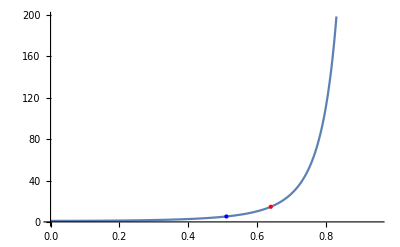

```mathematica
Show[
Plot[bigF[e],{e, 0, 0.95}],
Graphics[{PointSize[Large],Red,Point[{0.64,bigF[0.64]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,bigF[0.511]}]}]
]
```

```mathematica
{bigF[0.64],bigF[0.511]}
```

{14.6116,5.25036}

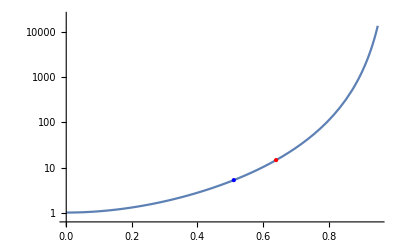

```mathematica
Show[
LogPlot[bigF[e],{e, 0, 0.95}, GridLines->Automatic],
Graphics[{PointSize[Large],Red,Point[{0.64,Log[bigF[0.64]]}]}],
Graphics[{PointSize[Large],Blue,Point[{0.511,Log[bigF[0.511]]}]}]
]
```

```mathematica
Solve[bigF[u]==100.0,{u}]
```

{{u→-1.04567-0.199658 ⅈ},{u→-1.04567+0.199658 ⅈ},{u→-0.793955},{u→0.793955},{u→1.04567-0.199658 ⅈ},{u→1.04567+0.199658 ⅈ}}

```mathematica
Log[2.7818]
```

1.0231

```mathematica
10^5.2
```

158489.